```mathematica
FPolar[P_]=Subscript[a,1](Sum[Subscript[P,i]^2, {i,1,3}])  +Subscript[a,11](Sum[Subscript[P,i]^4,{i,1,3}])+Subscript[a,12](Sum[Subscript[P,i]^2*Subscript[P,j]^2, {j,1,3}, {i,1,j-1}])+
Subscript[a,111](Sum[Subscript[P,i]^6, {i,1,3}])+1/2*Simplify[Subscript[a,112](Sum[Subscript[P,i]^2*(Subscript[P,j]^4+Subscript[P,k]^4)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+Subscript[a,123](Sum[Subscript[P,i]^2Subscript[P,j]^2Subscript[P,k]^2, {i,1,3},{j,1,i-1},{k,1,j-1}])+
Subscript[a,1111](Sum[Subscript[P,i]^8,{i,1,3}])+1/2*Simplify[Subscript[a,1112] (Sum[Subscript[P,i]^6*(Subscript[P,j]^2+Subscript[P,k]^2)(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]+
Subscript[a,1122] (Sum[Subscript[P,i]^4*Subscript[P,j]^4, {j,1,3}, {i,1,j-1}])+
1/2*Simplify[Subscript[a,1123] (Sum[Subscript[P,i]^4Subscript[P,j]^2Subscript[P,k]^2(Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3} ,{j,1,3}, {k,1,3}])]/.{False->0, True->1}

FElectrostriction[P_,u_]=-Subscript[q,11]*Sum[Subscript[u,i,i]Subscript[P,i]^2, {i,1,3}]-1/2Simplify[Subscript[q,12]*Sum[Subscript[u,i,i](Subscript[P,j]^2+Subscript[P,k]^2)( Boole[i≠j]&&Boole[i≠k]&&Boole[j≠k]),{i,1,3},{j,1,3},{k,1,3}]]-Subscript[q,44]*Sum[Subscript[u,i,j]*Subscript[P,i]*Subscript[P,j],{j,1,3}, {i,1,j-1}]/.{False->0, True->1}/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]};
FElastic[u_]=1/2*Subscript[c,11]*Sum[Subscript[u,i,i]^2 ,{i,1,3}]+Subscript[c,12]*Sum[Subscript[u,i,i]*Subscript[u,j ,j], {j,1,3}, {i,1,j-1}]+1/2*Subscript[c,44]*Sum[Subscript[u,i,j]^2,{j,1,3},{i,1,j-1}]/.{Subscript[u,1,1]-> Subscript[u,1],Subscript[u,2,2]-> Subscript[u,2],Subscript[u,3,3]-> Subscript[u,3],Subscript[u,2,3]-> Subscript[u,4],Subscript[u,1,3]-> Subscript[u,5],Subscript[u,1,2]-> Subscript[u,6]};
FGradient[P_]=Subscript[g,11]/2*Sum[Subscript[P, i,i]^2, {i,1,3}]+Subscript[g,12]*Sum[Subscript[P,i,i]Subscript[P,j,j],{j,1,3},{i,1,j-1}]+Subscript[g,44]/2*Sum[(Subscript[P,i,j]+Subscript[P,j,i])^2, {j,1,3},{i,1,j-1}];
FBulk[P_,u_]=FPolar[P]+FElectrostriction[P, u]+FElastic[u];
```

a_123 P_1^2 P_2^2 P_3^2+a_1 (P_1^2+P_2^2+P_3^2)+a_1123 P_1^2 P_2^2 P_3^2 (P_1^2+P_2^2+P_3^2)+a_12 (P_1^2 P_2^2+P_1^2 P_3^2+P_2^2 P_3^2)+a_11 (P_1^4+P_2^4+P_3^4)+a_1122 (P_1^4 P_2^4+P_1^4 P_3^4+P_2^4 P_3^4)+a_111 (P_1^6+P_2^6+P_3^6)+a_1111 (P_1^8+P_2^8+P_3^8)+a_112 (P_1^4 (P_2^2+P_3^2)+P_2^2 P_3^2 (P_2^2+P_3^2)+P_1^2 (P_2^4+P_3^4))+a_1112 (P_2^6 P_3^2+P_2^2 P_3^6+P_1^6 (P_2^2+P_3^2)+P_1^2 (P_2^6+P_3^6))

```mathematica
(*================================================================================================================================================================================*)
(* New Rules Functions to take Derivatives of subscripted notations. *)
SubToVariableRules={Subscript[P, 1,1]-> PG11,Subscript[P, 1,2]-> PG12, Subscript[P, 1,3]-> PG13, Subscript[P, 2,2]-> PG22, Subscript[P, 2,1]-> PG21, Subscript[P, 3,1]-> PG31, Subscript[P, 2,3]-> PG23, Subscript[P, 3,2]-> PG32, Subscript[P, 3,3]-> PG33,Subscript[P, 1] -> P1, Subscript[P, 2] -> P2,Subscript[P, 3] -> P3,
Subscript[u, 1]-> u1,Subscript[u, 2]-> u2,Subscript[u, 3]-> u3,Subscript[u, 4]-> u4,Subscript[u, 5]-> u5,Subscript[u, 6]-> u6};
VariableToSubRules={ PG11-> Subscript[P, 1,1],PG12-> Subscript[P, 1,2],PG13-> Subscript[P, 1,3],PG22-> Subscript[P, 2,2],PG21-> Subscript[P, 2,1],PG31-> Subscript[P, 3,1],PG23-> Subscript[P, 2,3],PG32-> Subscript[P, 3,2],PG33-> Subscript[P, 3,3],P1-> Subscript[P, 1],P2-> Subscript[P, 2],P3-> Subscript[P, 3],
u1-> Subscript[u, 1],u2-> Subscript[u, 2],u3-> Subscript[u, 3],u4-> Subscript[u, 4],u5-> Subscript[u, 5],u6-> Subscript[u, 6]};
CoefficientsToVariables={Subscript[a, 1]->a1,Subscript[a, 11]->a11, Subscript[a, 12]->a12,Subscript[a, 111]->a111,Subscript[a, 112]->a112,Subscript[a, 123]->a123,
Subscript[a, 1111]->a1111,Subscript[a, 1112]->a1112,Subscript[a, 1122]->a1122,Subscript[a, 1123]->a1123,
Subscript[c, 11]->c11,Subscript[c, 12]->c12,Subscript[c, 44]->c44,Subscript[q, 11]->q11,Subscript[q, 12]->q12,Subscript[q, 44]->q44};
ElectrostrictiveCoefficients={(-c12 q11+2 c11 q12)/(c11^2+c11 c12-2 c12^2)-> Q12, (c11 q11+c12 q11-4 c12 q12)/(c11^2+c11 c12-2 c12^2)-> Q11, q44/c44-> Q44};

(* THERMODYNAMIC COEFFICIENTS AND ELASTIC CONSTANTS *)WangCoefficients={ a1->3.61*10^5*(T-391),a11->-1.83*10^9+4*10^6*T,a12->-2.24*10^9+6.7*10^6*T,a111->1.39*10^10-3.2*10^7*T,a112->-2.2*10^9,a123->5.51*10^10,
a1111->4.84*10^10,a1112->2.53*10^11,a1122->2.80*10^11,a1123->9.35*10^10, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
TElasticConstants={c11-> 300*10^9,c12->109*10^9};
OElasticConstants={c11->150*10^9,c22->312*10^9,c33->150*10^9,c44->135*10^9,c12->100*10^9};
LiCoefficients={a1-> 4.124*10^5*(T-388),a11-> -2.097*10^8,a12->7.974*10^8,a111-> 1.294*10^9,a112-> -1.95*10^9,a123->-2.5*10^9,
a1111->3.863*10^10,a1112->2.529*10^10,a1122->1.637*10^10,a1123->1.367*10^10,c11->27.50*10^10,c12->17.90*10^10,c44->5.43*10^10, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};
BellCoefficients={a1->3.34*10^5*(T-381),a11->4.69*10^6*(T-393)-2.02*10^8,a12->-3.23*10^8,a111->-5.52*10^7*(T-393)+2.76*10^9,a112->4.47*10^9,a123->4.91*10^9,
c11->27.50*10^10,c12->17.90*10^10,c44->5.43*10^10, q11->14.20*10^9,q12->-0.74*10^9,q44->1.57*10^9};

(* Renormalization *)
RenormalizedParameters={A11->a11+(1/2*((c11 q11+c12 q11-2 c12 q12) q11)/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) q12)/((c11-c12) (c11+2 c12))), A12->a12+((2 Subscript[c, 12]^2 Subscript[q, 44]^2+Subscript[c, 12] (2 Subscript[c, 44] (Subscript[q, 11]^2+8 Subscript[q, 12]^2)-Subscript[c, 11] Subscript[q, 44]^2)-Subscript[c, 11] (8 Subscript[c, 44] Subscript[q, 12] (Subscript[q, 11]+Subscript[q, 12])+Subscript[c, 11] Subscript[q, 44]^2))/(2 (Subscript[c, 11]-Subscript[c, 12]) (Subscript[c, 11]+2 Subscript[c, 12]) Subscript[c, 44])) };
NormalizedParameters={A11->a11-(1/2*((c11 q11+c12 q11-2 c12 q12) q11)/(c11^2+c11 c12-2 c12^2)+((-c12 q11+c11 q12) q12)/((c11-c12) (c11+2 c12))), A12->a12-((2 Subscript[c, 12]^2 Subscript[q, 44]^2+Subscript[c, 12] (2 Subscript[c, 44] (Subscript[q, 11]^2+8 Subscript[q, 12]^2)-Subscript[c, 11] Subscript[q, 44]^2)-Subscript[c, 11] (8 Subscript[c, 44] Subscript[q, 12] (Subscript[q, 11]+Subscript[q, 12])+Subscript[c, 11] Subscript[q, 44]^2))/(2 (Subscript[c, 11]-Subscript[c, 12]) (Subscript[c, 11]+2 Subscript[c, 12]) Subscript[c, 44])) };

(* ADDITIONAL FUNCTIONS *)
(* Shows an indeterminate progress bar and elapsed time,updating a few times per second. *)
SetAttributes[ShowProgress,HoldAll];
ShowProgress[a_]:=With[{progressStartTime=AbsoluteTime[]},Monitor[a,Dynamic[Refresh[Row[{ProgressIndicator[Dynamic[Clock[]],Indeterminate],AbsoluteTime[]-progressStartTime}," "],UpdateInterval->0.25]]]];
```

```mathematica
(*================================================================================================================================================================================*)
(* Determining equilibrium solutions for the strain *)
FStrainDerivative[P_,u_]={Collect[D[FBulk[P,u]/.SubToVariableRules, u1], u1, Simplify],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u2]], u2],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u3]], u3],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u4]], u4], Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u5]], u5],Collect[Simplify[D[FBulk[P,u]/.SubToVariableRules, u6]], u6]}/.CoefficientsToVariables/.ElectrostrictiveCoefficients;

StrainSolutions=Collect[Solve[{(FStrainDerivative[P,u][[1]])==0,(FStrainDerivative[P,u][[2]])==0,
(FStrainDerivative[P,u][[3]])==0,(FStrainDerivative[P,u][[4]])==0,
(FStrainDerivative[P,u][[5]])==0,(FStrainDerivative[P,u][[6]])==0},{u1,u2,u3, u4,u5,u6}], {P1,P2,P3},Simplify]/.ElectrostrictiveCoefficients

StrainSolutionSimplified={{u1->P1^2*Q11+Q12*(P2^2+P3^2), u2->P2^2 Q11+(P1^2+P3^2) Q12, u3->P3^2 Q11+(P1^2+P2^2) Q12, u4->P2 P3 Q44,u5->P1 P3 Q44,u6->P1 P2 Q44}}
```

{{u1→(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P1^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u2→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u3→(P1^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P2^2 (-c12 q11+c11 q12))/((c11-c12) (c11+2 c12))+(P3^2 (c11 q11+c12 q11-2 c12 q12))/(c11^2+c11 c12-2 c12^2),u4→P2 P3 Q44,u5→P1 P3 Q44,u6→P1 P2 Q44}}

{{u1→P1^2 Q11+(P2^2+P3^2) Q12,u2→P2^2 Q11+(P1^2+P3^2) Q12,u3→P3^2 Q11+(P1^2+P2^2) Q12,u4→P2 P3 Q44,u5→P1 P3 Q44,u6→P1 P2 Q44}}

```mathematica
(*================================================================================================================================================================================*)
(* Polarization of the Tetragonal Phase *)
TetragonalFreeEnergyDeriv=D[FPolar[P]/.SubToVariableRules, P3]/.P1->0/.P2->0;
(* Strain-Dependent Tetragonal Phase *)
TetragonalSolution=Simplify[Solve[(TetragonalFreeEnergyDeriv==0&&P3≠0) , P3]];

(* The Sixth Order Solutions *)
TetragonalPolarizationwoStrain=√((-Subscript[a, 11]+√(Subscript[a, 11]^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]));
TetragonalPolarization=√((-A11+√(A11^2-3 Subscript[a, 1] Subscript[a, 111]))/(3 Subscript[a, 111]));
Plot[{TetragonalPolarizationwoStrain/.RenormalizedParameters/.CoefficientsToVariables/.BellCoefficients,
      TetragonalPolarization/.RenormalizedParameters/.CoefficientsToVariables/.BellCoefficients} ,{T,200,400}];
(* The Eighth Order Plot of the Tetragonal Polarization *)
Plot[{P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
      P3/.TetragonalSolution[[2,1]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients} ,{T,200,400}];
```

```mathematica
(*================================================================================================================================================================================*)
(* Polarization of the Orthorhombic Phase *)
P=.
OrthorhombicFreeEnergyDeriv=D[FPolar[P]/.SubToVariableRules, P3]/.P2->0/.P1->P/Sqrt[2]/.P3->P/Sqrt[2]
(* Strain-Dependent Orthorhombic Phase *)
(* OrthorhombicSolution=Simplify[Solve[(OrthorhombicFreeEnergyDeriv==0&&P≠0) , P]]; *)

OrthorhombicSolution=ShowProgress[Solve[(OrthorhombicFreeEnergyDeriv==0&&P≠0) , P]];

(* The Sixth Order Solutions *)
OrthorhombicPolarizationwoStrain=(√((-2 Subscript[a, 11]-Subscript[a, 12]+√(4 Subscript[a, 11]^2+4 Subscript[a, 11] Subscript[a, 12]+Subscript[a, 12]^2-12 Subscript[a, 1] (Subscript[a, 111]+Subscript[a, 112])))/(Subscript[a, 111]+Subscript[a, 112])))/(√3);
OrthorhombicPolarization=(√((-2 A11-A12+√(4 A11^2+4 A11 A12+A12^2-12 Subscript[a, 1] (Subscript[a, 111]+Subscript[a, 112])))/(Subscript[a, 111]+Subscript[a, 112])))/(√3);
Plot[{OrthorhombicPolarizationwoStrain/.RenormalizedParameters/.CoefficientsToVariables/.BellCoefficients,
      OrthorhombicPolarization/.RenormalizedParameters/.CoefficientsToVariables/.BellCoefficients} ,{T,200,400}];
(* The Eighth Order Plot of the Orthorhombic Polarization *)
(* Comparison accounting for strain and w/o strain *)
Plot[{P/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
      P/.OrthorhombicSolution[[2,1]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients} ,{T,200,400}];
(* All solutions graphed *)
Plot[{P/.OrthorhombicSolution[[1,1]]/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
P/.OrthorhombicSolution[[3,1]]/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[4,1]]/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[5,1]]/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[6,1]]/.CoefficientsToVariables/.LiCoefficients}, {T,200,400}];
```

√2 P a_1+√2 P^3 a_11+(P^3 a_12)/(√2)+(3 P^5 a_111)/(2 √2)+(3 P^5 a_112)/(2 √2)+(P^7 a_1111)/(√2)+(P^7 a_1112)/(√2)+(P^7 a_1122)/(2 √2)

```mathematica
(*================================================================================================================================================================================*)(* Polarization of the Monoclinic Phase *)
MonoclinicFreeEnergyDerivP1=Simplify[D[FPolar[P]/.SubToVariableRules, P1]/(2*P1)/.P2->0];
MonoclinicFreeEnergyDerivP1Squared=MonoclinicFreeEnergyDerivP1/.P1-> P1^(1/2)/.P3-> P3^(1/2);
MonoclinicFreeEnergyDerivP3=Simplify[D[FPolar[P]/.SubToVariableRules, P3]/(2*P3)/.P2->0];
MonoclinicFreeEnergyDerivP3Squared=MonoclinicFreeEnergyDerivP3/.P1-> P1^(1/2)/.P3-> P3^(1/2);
(* Second Derivatives of the Monoclinic Phase to determine Phase Stability *)
MonoclinicFreeEnergyDerivP1P1=Simplify[D[D[FPolar[P]/.SubToVariableRules, P1], P1]/.P2->0];
MonoclinicFreeEnergyDerivP1P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P1]/.P2->0];
MonoclinicFreeEnergyDerivP3P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P3]/.P2->0];
Simplify[MonoclinicFreeEnergyDerivP1Squared/.CoefficientsToVariables/.LiCoefficients];
(*_______________________________________________________________________________________________________________________________________________________________________________*)
(* STRAIN-DEPENDENT MONOCLINIC PHASE *)
(* This Attempt deals with the square of the polarization to reduce the number of solutions since plus-minus only gives direction of polarizaiton vector. *)
(* ANALYTICAL *)
(*
MonoclinicSolutionAnalytical=ShowProgress[Simplify[Solve[MonoclinicFreeEnergyDerivP1Squared==0&&P1≠0 &&
  MonoclinicFreeEnergyDerivP3Squared==0&&P3≠0&&P1≠P3, {P1,P3}]]]
*)
(* NUMERICAL *)
(* There are six solutions for the following numerical result, giving 12 possible orientations for solutions to the polarization. *)
MonoclinicSolution=Simplify[Solve[Simplify[MonoclinicFreeEnergyDerivP1Squared/.CoefficientsToVariables/.LiCoefficients]==0&&P1≠0 &&
                                                                    Simplify[MonoclinicFreeEnergyDerivP3Squared/.CoefficientsToVariables/.LiCoefficients]==0&&P3≠0&&P1≠P3, {P1,P3}]];

(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* THE EIGHTH ORDER PLOTS OF THE MONOCLINIC POLARIZATION *)
(* Solutions #1 and #4 gave zero polarization magnitude (non-physical) *)
(* Solutions #5 and #6 have only real polarization magnitude values T > 309 K *)
(* MAGNITUDE OF POLARIZATION *)
Plot[Sqrt[(P1/.MonoclinicSolution[[1,1]])+(P3/.MonoclinicSolution[[1,2]])],{T,250,320}];
Plot[Sqrt[(P1/.MonoclinicSolution[[2,1]])+(P3/.MonoclinicSolution[[2,2]])],{T,250,320}];
Plot[Sqrt[(P1/.MonoclinicSolution[[3,1]])+(P3/.MonoclinicSolution[[3,2]])],{T,250,320}];
Plot[Sqrt[(P1/.MonoclinicSolution[[4,1]])+(P3/.MonoclinicSolution[[4,2]])],{T,250,320}];
Plot[Sqrt[(P1/.MonoclinicSolution[[5,1]])+(P3/.MonoclinicSolution[[5,2]])],{T,250,320}];
Plot[Sqrt[(P1/.MonoclinicSolution[[6,1]])+(P3/.MonoclinicSolution[[6,2]])],{T,250,320}];

(* COMPONENTS OF POLARIZATION *)
(* Solutions #1 and #4 have an imaginary solution for either P1 or P3, respectively. *)
(* Solutions for #5 and #6 are both imaginary solutions for P1 and P3. *)
Plot[{Sqrt[P1/.MonoclinicSolution[[1,1]]],Sqrt[P3/.MonoclinicSolution[[1,2]]]},{T,200,400}];
Plot[{Sqrt[P1/.MonoclinicSolution[[2,1]]],Sqrt[P3/.MonoclinicSolution[[2,2]]]},{T,200,400}];
Plot[{Sqrt[P1/.MonoclinicSolution[[3,1]]],Sqrt[P3/.MonoclinicSolution[[3,2]]]},{T,200,400}];
Plot[{Sqrt[P1/.MonoclinicSolution[[4,1]]],Sqrt[P3/.MonoclinicSolution[[4,2]]]},{T,200,400}];
Plot[{Sqrt[P1/.MonoclinicSolution[[5,1]]],Sqrt[P3/.MonoclinicSolution[[5,2]]]},{T,200,400}];
Plot[{Sqrt[P1/.MonoclinicSolution[[6,1]]],Sqrt[P3/.MonoclinicSolution[[6,2]]]},{T,200,400}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

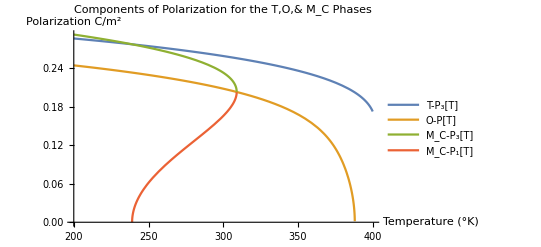

```mathematica
(*================================================================================================================================================================================*)
(* Comparing the Polarization Graphs for each Phase *)
(* MAGNITUDE OF POLARIZATION *)
Plot[{P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,Sqrt[(P1/.MonoclinicSolution[[2,1]])+(P3/.MonoclinicSolution[[2,2]])],Sqrt[(P1/.MonoclinicSolution[[3,1]])+(P3/.MonoclinicSolution[[3,2]])]},{T,200,400}, PlotLegends->{"T-P[T]", "O-P[T]","M_C-P[T]"}, AxesLabel->{"Temperature (°K)", "Polarization C/m^2"}, PlotLabel->"Polarization Magnitude for the T,O,& M_C Phases"];
(* COMPONENTS OF POLARIZATION *)
Plot[{P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
       (P/Sqrt[2])/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
       Sqrt[P1/.MonoclinicSolution[[3,1]]/.CoefficientsToVariables/.LiCoefficients],
       Sqrt[P3/.MonoclinicSolution[[3,2]]/.CoefficientsToVariables/.LiCoefficients]},  {T,200,400}, 
      PlotLegends->{"T-P_3[T]", "O-P[T]","M_C-P_3[T]","M_C-P_1[T]"}, AxesLabel->{"Temperature (°K)", "Polarization C/m^2"}, 
      PlotLabel->"Components of Polarization for the T,O,& M_C Phases"]
(* Plotting the third solution for the monoclinic phase to test the other case P1->P3,P3->P1 *)
Plot[{P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
        (P/Sqrt[2])/.OrthorhombicSolution[[2,1]]/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients,
        Sqrt[P1/.MonoclinicSolution[[3,1]]/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients],
        Sqrt[P3/.MonoclinicSolution[[3,2]]/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients]},{T,200,400},   
       PlotLegends->{"T-P_3[T]", "O-P[T]","M_C-P_1[T]","M_C-P_3[T]"}, AxesLabel->{"Temperature (°K)", "Polarization C/m^2"}, 
       PlotLabel->"Components of Polarization for the T,O,& M_C Phases"];
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* COMPARING THE STRAIN-INDEPENDENT CASE FOR EACH PHASE *)
(* The Monoclinic Solutions become imaginary when considering the Strain-independent case for temperatures > 192° Kelvin *)
Plot[{P3/.TetragonalSolution[[2,1]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients,P/.OrthorhombicSolution[[2,1]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients,Sqrt[P1/.MonoclinicSolution[[2,1]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients],Sqrt[P3/.MonoclinicSolution[[2,2]]/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.RenormalizedParameters/.CoefficientsToVariables/.LiCoefficients]},{T,200,400},   PlotLegends->{"T-P_3[T]", "O-P[T]","M_C-P_1[T]","M_C-P_3[T]"}, AxesLabel->{"Temperature (°K)", "Polarization C/m^2"}, PlotLabel->"Components of Polarization for the T,O,& M_C Phases"];
```

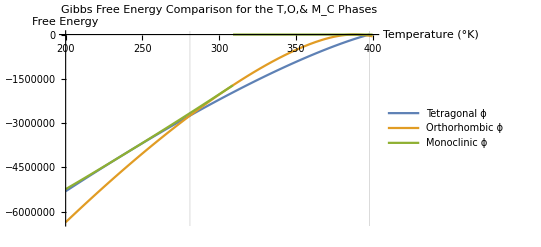

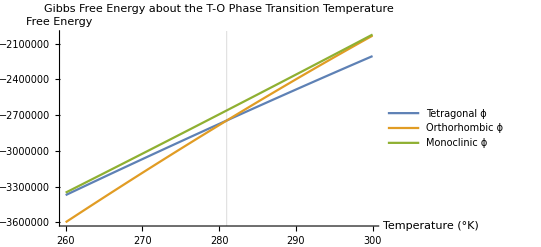

```mathematica
(*================================================================================================================================================================================*)
(* FREE ENERGY ANALYSIS *)
(* Using the solutions for the order parameter (polarization) the free energy as a function of temperature can be compared between the different phases to determine the order of phase transition as well as the phase transition temperature. *)
TetragonalFreeEnergy=FPolar[P]/.SubToVariableRules/.P2->0/.P1->0;
TetragonalFreeEnergywoStrain=FPolar[P]/.SubToVariableRules/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.NormalizedParameters/.P2->0/.P1->0;
OrthorhombicFreeEnergy=FPolar[P]/.SubToVariableRules/.P2->0/.P1->P/Sqrt[2]/.P3->P/Sqrt[2];
OrthorhombicFreeEnergywoStrain=FPolar[P]/.SubToVariableRules/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.NormalizedParameters/.P2->0/.P1->P/Sqrt[2]/.P3->P/Sqrt[2];
MonoclinicFreeEnergy=FPolar[P]/.SubToVariableRules/.P2->0;
MonoclinicFreeEnergywoStrain=FPolar[P]/.SubToVariableRules/.Subscript[a, 11]->A11/.Subscript[a, 12]->A12/.NormalizedParameters/.P2->0;
MonoclinicFreeEnergyEvaluated=MonoclinicFreeEnergy/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.MonoclinicSolution[[3,1]]/.MonoclinicSolution[[3,2]]/.CoefficientsToVariables/.  LiCoefficients;
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* COMPARING THE FREE ENERGY GRAPHS FOR STRAIN-INDEPENDENT CASE *)
Plot[{TetragonalFreeEnergywoStrain/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
       OrthorhombicFreeEnergywoStrain/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
       MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[2,1]]/.MonoclinicSolution[[2,2]]/.CoefficientsToVariables/.LiCoefficients,
       MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[3,1]]/.MonoclinicSolution[[3,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
(* The free energy for solutions #1 and #4 correspond to that of the O phase. *)
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[1,1]]/.MonoclinicSolution[[1,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[2,1]]/.MonoclinicSolution[[2,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[3,1]]/.MonoclinicSolution[[3,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[4,1]]/.MonoclinicSolution[[4,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[5,1]]/.MonoclinicSolution[[5,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
Plot[{MonoclinicFreeEnergywoStrain/.MonoclinicSolution[[6,1]]/.MonoclinicSolution[[6,2]]/.CoefficientsToVariables/.LiCoefficients},{T,200,400}];
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* COMPARING THE FREE ENERGY GRAPHS FOR STRAIN-DEPENDENT CASE *)
Plot[{TetragonalFreeEnergy/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
        OrthorhombicFreeEnergy/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients ,
        Piecewise[{{MonoclinicFreeEnergyEvaluated, T≤ 309}}]}, {T,200,400},   
           PlotRange-> {0,-8*10^6},PlotLegends->{"Tetragonal ϕ", "Orthorhombic ϕ","Monoclinic ϕ"}, AxesLabel->{"Temperature (°K)", "Free Energy"}, 
	  PlotLabel->"Gibbs Free Energy Comparison for the T,O,& M_C Phases",GridLines-> {{281, 398},{0}}]
Plot[{TetragonalFreeEnergy/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
        OrthorhombicFreeEnergy/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients ,
        MonoclinicFreeEnergy/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.MonoclinicSolution[[3,1]]/.MonoclinicSolution[[3,2]]/.CoefficientsToVariables/.LiCoefficients}, {T,260,300},   
           PlotRange-> Automatic,PlotLegends->{"Tetragonal ϕ", "Orthorhombic ϕ","Monoclinic ϕ"}, AxesLabel->{"Temperature (°K)", "Free Energy"}, 
	  PlotLabel->"Gibbs Free Energy about the T-O Phase Transition Temperature",GridLines-> {{281},{0}}]
(* MonoclinicFreeEnergy/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.MonoclinicSolution[[2,1]]/.MonoclinicSolution[[2,2]]/.CoefficientsToVariables/.LiCoefficients, *)
(*_________________________________________________________________________________________________________________________________________________________*)
```

Entropy of C-T and T-O in J/m^3

Entropy of Monoclinic Phase

Entropy of C-T and T-O in cal/mol

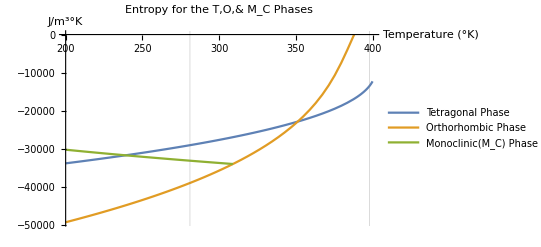

```mathematica
(*================================================================================================================================================================================*)
(* Determining the Entropy of the phase transitions *)
EntropyCT=P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients/.T-> 388;
EntropyT=P3/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients/.T-> 283;
EntropyO=P/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients/.T->283;
EntropyTMc=((P1/.MonoclinicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients/.T-> 283)+
(P3/.MonoclinicSolution[[2,2]]/.CoefficientsToVariables/.LiCoefficients/.T-> 283))^(1/2);
EntropyOMc=((P1/.MonoclinicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients/.T-> 283)+
(P3/.MonoclinicSolution[[2,2]]/.CoefficientsToVariables/.LiCoefficients/.T-> 283))^(1/2);

(* δS=δP^2/(2ϵ_o*C)
1/(2*8.85E-12*1.7*10^5)*(δP)^2 *)
"Entropy of C-T and T-O in J/m^3"
1/(2*8.85*10^-12*1.7*10^5)*EntropyCT^2;
1/(2*8.85*10^-12*1.7*10^5)*Abs[EntropyT^2-EntropyO^2];
"Entropy of Monoclinic Phase"
1/(2*8.85*10^-12*1.7*10^5)*Abs[EntropyT^2-EntropyTMc^2];
%*(9.16*10^-6);
1/(2*8.85*10^-12*1.7*10^5)*Abs[EntropyO^2-EntropyOMc^2];
%*(9.16*10^-6);
"Entropy of C-T and T-O in cal/mol"
13635.6*(9.16*10^-6);
8086.62*(9.16*10^-6);
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* DETERMINING THE TEMPERATURE DEPENDENCE OF THE ENTROPY FOR EACH PHASE *)
T=.
EntropyS=-D[FBulk[P,u]/.StrainSolutions/.CoefficientsToVariables/.LiCoefficients, T]/.SubToVariableRules;
EntropySMonoclinicEvaluated=EntropyS/.P2-> 0/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.{MonoclinicSolution[[2,1]], MonoclinicSolution[[2,2]]}/.CoefficientsToVariables/.LiCoefficients;
Plot[{EntropyS/.{P1->0,P2-> 0}/.TetragonalSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
         EntropyS/.{P1->P/Sqrt[2],P3->P/Sqrt[2],P2-> 0}/.OrthorhombicSolution[[2,1]]/.CoefficientsToVariables/.LiCoefficients,
         Piecewise[{{EntropySMonoclinicEvaluated, T≤309}}]},{T,200,400}, 
        PlotRange-> {0,-51000},GridLines-> {{281, 398},{0}},PlotLegends->{"Tetragonal Phase","Orthorhombic Phase","Monoclinic(M_C) Phase"}, AxesLabel->{"Temperature (°K)", "J/m^3°K"}, PlotLabel->"Entropy for the T,O,& M_C Phases"]
(* Conversion Factor 9.16*10^-6 *)
```

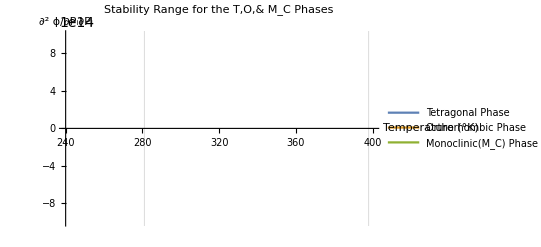

```mathematica
(*_________________________________________________________________________________________________________________________________________________________________________________*)
(* DETERMINING TEMPERATURE INTERVAL OF STABILITY FOR EACH PHASE *)
(* Second Derivatives of the Monoclinic Phase to determine Phase Stability *)
MonoclinicFreeEnergyDerivP1P1=Simplify[D[D[FPolar[P]/.SubToVariableRules, P1], P1]/.P2->0]/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.{MonoclinicSolution[[2,1]], MonoclinicSolution[[2,2]]};
MonoclinicFreeEnergyDerivP1P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P1]/.P2->0]/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.{MonoclinicSolution[[2,1]], MonoclinicSolution[[2,2]]};
MonoclinicFreeEnergyDerivP3P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P3]/.P2->0]/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.{MonoclinicSolution[[2,1]], MonoclinicSolution[[2,2]]};
MonoclinicFreeEnergyDerivP2P2=Simplify[D[D[FPolar[P]/.SubToVariableRules, P2], P2]/.P2->0]/.{P1-> P1^(1/2), P3-> P3^(1/2)}/.{MonoclinicSolution[[2,1]], MonoclinicSolution[[2,2]]};
(* Second Derivatives of the Tetragonal Phase to determine Phase Stability *)
TetragonalFreeEnergyDerivP3P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P3]/.P1->0/.P2->0]/.TetragonalSolution[[2,1]];
TetragonalFreeEnergyDerivP1P1=Simplify[D[D[FPolar[P]/.SubToVariableRules, P1], P1]/.P1->0/.P2->0]/.TetragonalSolution[[2,1]];
TetragonalFreeEnergyDerivP2P2=Simplify[D[D[FPolar[P]/.SubToVariableRules, P2], P2]/.P1->0/.P2->0]/.TetragonalSolution[[2,1]];
(* Second Derivatives of the Orthorhombic Phase to determine Phase Stability *)
OrthorhombicFreeEnergyDerivP3P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P3]/.P3->P/Sqrt[2]/.P1->P/Sqrt[2]/.P2->0]/.OrthorhombicSolution[[2,1]];
OrthorhombicFreeEnergyDerivP1P1=Simplify[D[D[FPolar[P]/.SubToVariableRules, P1], P1]/.P3->P/Sqrt[2]/.P1->P/Sqrt[2]/.P2->0]/.OrthorhombicSolution[[2,1]];
OrthorhombicFreeEnergyDerivP1P3=Simplify[D[D[FPolar[P]/.SubToVariableRules, P3], P1]/.P3->P/Sqrt[2]/.P1->P/Sqrt[2]/.P2->0]/.OrthorhombicSolution[[2,1]];
OrthorhombicFreeEnergyDerivP2P2=Simplify[D[D[FPolar[P]/.SubToVariableRules, P2], P2]/.P3->P/Sqrt[2]/.P1->P/Sqrt[2]/.P2->0]/.OrthorhombicSolution[[2,1]];

StabilityRelationMonoclinic=MonoclinicFreeEnergyDerivP1P1*MonoclinicFreeEnergyDerivP3P3-MonoclinicFreeEnergyDerivP1P3^2;
StabilityRelationOrthorhombic=OrthorhombicFreeEnergyDerivP1P1*OrthorhombicFreeEnergyDerivP3P3-OrthorhombicFreeEnergyDerivP1P3^2;
StabilityRelationTetragonal= TetragonalFreeEnergyDerivP1P1*TetragonalFreeEnergyDerivP3P3;
Plot[{StabilityRelationTetragonal/.CoefficientsToVariables/.LiCoefficients,
        StabilityRelationOrthorhombic/.CoefficientsToVariables/.LiCoefficients,
        StabilityRelationMonoclinic/.CoefficientsToVariables/.LiCoefficients}, {T,240,400}, PlotRange-> {-2*10^16,4*10^16},   
          PlotLegends->{"Tetragonal Phase","Orthorhombic Phase","Monoclinic(M_C) Phase"}, AxesLabel->{"Temperature (°K)", "∂^2 ϕ/∂P_i∂P_j"},
          PlotLabel->"Stability Range for the T,O,& M_C Phases", GridLines->{{281, 398},{0}}]
```